## 2D square lattice (Spin-less)

### Model

```mathematica
(****************************************** Function to generate a supercell ******************************************)
GenerateSupercell[atoms_,a1_,a2_,nx_,ny_]:=Module[{supercell},
supercell=Flatten[Table[(#+n a1+m a2)&/@atoms,{n,0,nx-1},{m,0,ny-1}],2];
supercell];
GroupAtomsByDistance[coordinates_,minDist_,maxDist_]:=Module[{pairs},pairs=Select[Subsets[coordinates,{2}],(*Generate all pairs of coordinates*)minDist<EuclideanDistance[#[[1]],#[[2]]]<maxDist&];
pairs];

(******************************************  Generate a NxN supercell and Plot *****************************************)
atomPositions = {{0,0}(*,{0,1},{1,0},{1,1}*)};
ax = {1,0};
ay = {0,1};
nx=5; ny=5;
supercellCoordinates=SortBy[GenerateSupercell[atomPositions,ax,ay,nx,ny],First];
hoppings=GroupAtomsByDistance[supercellCoordinates,0.9,1.1];

Show[Table[Graphics3D[{Red,Specularity[White,20],Sphere[Append[supercellCoordinates[[i]],0],0.2]},Boxed->False],{i,1,Length@supercellCoordinates}],Table[Graphics3D[{RGBColor[0.04,0.38,1.],Specularity[White,20],Cylinder[Append[#,0]&/@hoppings[[i,1;;2]],0.07]},Boxed->False],{i,1,Length@hoppings}],Table[Graphics3D[Text[Style[i,20,White],Append[supercellCoordinates[[i]],0]]],{i,1,Length[supercellCoordinates]}],ViewPoint->Above,ImageSize->400]

(******************************* nearest neighbors *******************************)
nearestNeighbors[latticeCoordinates_]:=Table[{point,Select[latticeCoordinates,0<EuclideanDistance[#,point]<= 1.1&]},{point,latticeCoordinates}]
nearestNeighborsIndex[latticeCoordinates_]:=Table[{First@First@Position[latticeCoordinates,point],Flatten[First@Position[latticeCoordinates,#]&/@Select[latticeCoordinates,0<EuclideanDistance[#,point]<=1.1&]]},{point,latticeCoordinates}]
NNH=nearestNeighbors[supercellCoordinates];
NNHI=nearestNeighborsIndex[supercellCoordinates]
```

-Graphics3D-

{{1,{2,6}},{2,{1,3,7}},{3,{2,4,8}},{4,{3,5,9}},{5,{4,10}},{6,{1,7,11}},{7,{2,6,8,12}},{8,{3,7,9,13}},{9,{4,8,10,14}},{10,{5,9,15}},{11,{6,12,16}},{12,{7,11,13,17}},{13,{8,12,14,18}},{14,{9,13,15,19}},{15,{10,14,20}},{16,{11,17,21}},{17,{12,16,18,22}},{18,{13,17,19,23}},{19,{14,18,20,24}},{20,{15,19,25}},{21,{16,22}},{22,{17,21,23}},{23,{18,22,24}},{24,{19,23,25}},{25,{20,24}}}

### Transmission

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

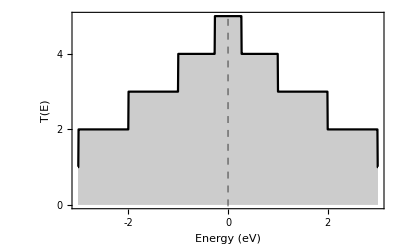

```mathematica
(******************************************* System Parameters ************************************************)
onsiteChannel=0; tHorizontalChannel=1; tVerticalChannel = 1;
τSC = 1.; τCD = τSC; 
onsiteSource=0; tHorizontalSource=1.; tVerticalSource = 1;
onsiteDrain=onsiteSource; tHorizontalDrain=tHorizontalSource; tVerticalDrain = tVerticalSource ;
η=0.00001;
surfaceElements1=Sort@Table[i,{i,1,5}];

(****************************************** system hamiltonian ********************************)
surfaceElements= Sort@Join[surfaceElements1,Table[Length@latticeCoordinates-surfaceElements1[[i]]+1,{i,1,Length@surfaceElements1}]];
Hamiltonian = Table[If[r==c ,onsiteChannel,If[MemberQ[NNHI[[r,2]],c],tHorizontalChannel,0]],{r, 1, Length@supercellCoordinates},{c, 1, Length@supercellCoordinates}];

(***************************************** Couplings ******************************************)
τSource = Table[If[PossibleZeroQ[Hamiltonian[[r,c+Max[surfaceElements1]]]],0,τSC],{r,surfaceElements1},{c,surfaceElements1}]; (*Coupling between source to channel*)
τDrain = τSource;

(**********************************Leads******************************************)
alphaSource =Table[If[r==c,onsiteSource,If[MemberQ[NNHI[[r,2]],c],tHorizontalSource,0]],{r, 1, Length@surfaceElements1},{c, 1, Length@surfaceElements1}];
alphaDrain= alphaSource ;

τ0Source=Table[If[PossibleZeroQ[Hamiltonian[[r,c+Max[surfaceElements1]]]],0,tHorizontalSource],{r,surfaceElements1},{c,surfaceElements1}];
τ0Drain=τ0Source;

Map[MatrixForm,{Hamiltonian,τSource, alphaSource, τ0Source}];

E1=0.;
transmission =ParallelTable[
(******************************************* Self energy for Source ************************************************)
gS11=Inverse[(E1+ⅈ η) IdentityMatrix[Length@alphaSource ]-alphaSource ]; (*Surface Green's function*)
GS11=Array[x,{Length@alphaSource,Length@alphaSource}]; (*Solve dyson equation*)
f=(gS11.ConjugateTranspose[τ0Source].GS11.τ0Source-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@alphaSource *Length@alphaSource }]];
ΣS = ArrayFlatten[Table[If[i==j==1,ConjugateTranspose[τSource].Partition[Values[sol],{Length@τSource}].τSource,0],{i,1,Length@Hamiltonian-(Length@surfaceElements1-1)},{j,1,Length@Hamiltonian-(Length@surfaceElements1-1)}]];
ΓS =-2Im[ΣS];
(******************************************* Self energy for Drain ************************************************)
gS11=Inverse[(E1+ⅈ η) IdentityMatrix[Length@alphaDrain]-alphaDrain ]; (*Surface Green's function*)
GS11=Array[x,{Length@alphaDrain,Length@alphaDrain}]; (*Solve dyson equation*)
f=(gS11.τ0Drain.GS11.ConjugateTranspose[τ0Drain]-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@alphaDrain*Length@alphaDrain }]];
ΣD = ArrayFlatten[Table[If[i==j==Length@Hamiltonian-(Length@surfaceElements1-1),τDrain.Partition[Values[sol],{Length@τDrain}].ConjugateTranspose[τDrain],0],{i,1,Length@Hamiltonian-(Length@surfaceElements1-1)},{j,1,Length@Hamiltonian-(Length@surfaceElements1-1)}]];
ΓD=-2Im[ΣD];
(*Print[ΣS //Length," ",ΣD//Length," ",ΓS//Length," ",ΓD//Length," ",Length@Hamiltonian]*)
(*Print[ΣS //MatrixForm,ΣD//MatrixForm,ΓS//MatrixForm,ΓD//MatrixForm]*)
(******************************************* Green's function and Transmission ************************************************)
GR=Inverse[E1 IdentityMatrix[Length@Hamiltonian]-Hamiltonian-ΣS-ΣD];
GA=ConjugateTranspose[GR];
{E1, Chop[ Tr[ΓS.GR.ΓD.GA]]},{E1,-3.01,3.01,0.0057}];

tickFunction=Charting`ScaledTicks[{Identity,Identity},"TicksLength"->{.02,.01}][##,{5,1}]&;
ListLinePlot[transmission,Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Darker[Black]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]]
Map[MatrixForm,{ΓS,ΓD}];
```

## 2D square lattice (spin-full )

### Model

```mathematica
(****************************************** Function to generate a supercell ******************************************)
GenerateSupercell[atoms_,a1_,a2_,nx_,ny_]:=Module[{supercell},
supercell=Flatten[Table[(#+n a1+m a2)&/@atoms,{n,0,nx-1},{m,0,ny-1}],2];
supercell];
GroupAtomsByDistance[coordinates_,minDist_,maxDist_]:=Module[{pairs},pairs=Select[Subsets[coordinates,{2}],(*Generate all pairs of coordinates*)minDist<EuclideanDistance[#[[1]],#[[2]]]<maxDist&];
pairs];

(******************************************  Generate a NxN supercell and Plot *****************************************)
atomPositions = {{0,0}(*,{0,1},{1,0},{1,1}*)};
ax = {1,0};
ay = {0,1};
nx=5; ny=5;
supercellCoordinates=SortBy[GenerateSupercell[atomPositions,ax,ay,nx,ny],First];
hoppings=GroupAtomsByDistance[supercellCoordinates,0.9,1.1];

Show[Table[Graphics3D[{Red,Specularity[White,20],Sphere[Append[supercellCoordinates[[i]],0],0.2]},Boxed->False],{i,1,Length@supercellCoordinates}],Table[Graphics3D[{RGBColor[0.04,0.38,1.],Specularity[White,20],Cylinder[Append[#,0]&/@hoppings[[i,1;;2]],0.07]},Boxed->False],{i,1,Length@hoppings}],Table[Graphics3D[Text[Style[i,20,White],Append[supercellCoordinates[[i]],0]]],{i,1,Length[supercellCoordinates]}],ViewPoint->Above,ImageSize->400]

(******************************* nearest neighbors *******************************)
nearestNeighbors[latticeCoordinates_]:=Table[{point,Select[latticeCoordinates,0<EuclideanDistance[#,point]<= 1.1&]},{point,latticeCoordinates}]
nearestNeighborsIndex[latticeCoordinates_]:=Table[{First@First@Position[latticeCoordinates,point],Flatten[First@Position[latticeCoordinates,#]&/@Select[latticeCoordinates,0<EuclideanDistance[#,point]<=1.1&]]},{point,latticeCoordinates}]
NNH=nearestNeighbors[supercellCoordinates];
NNHI=nearestNeighborsIndex[supercellCoordinates]
```

-Graphics3D-

{{1,{2,6}},{2,{1,3,7}},{3,{2,4,8}},{4,{3,5,9}},{5,{4,10}},{6,{1,7,11}},{7,{2,6,8,12}},{8,{3,7,9,13}},{9,{4,8,10,14}},{10,{5,9,15}},{11,{6,12,16}},{12,{7,11,13,17}},{13,{8,12,14,18}},{14,{9,13,15,19}},{15,{10,14,20}},{16,{11,17,21}},{17,{12,16,18,22}},{18,{13,17,19,23}},{19,{14,18,20,24}},{20,{15,19,25}},{21,{16,22}},{22,{17,21,23}},{23,{18,22,24}},{24,{19,23,25}},{25,{20,24}}}

### Transmission

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

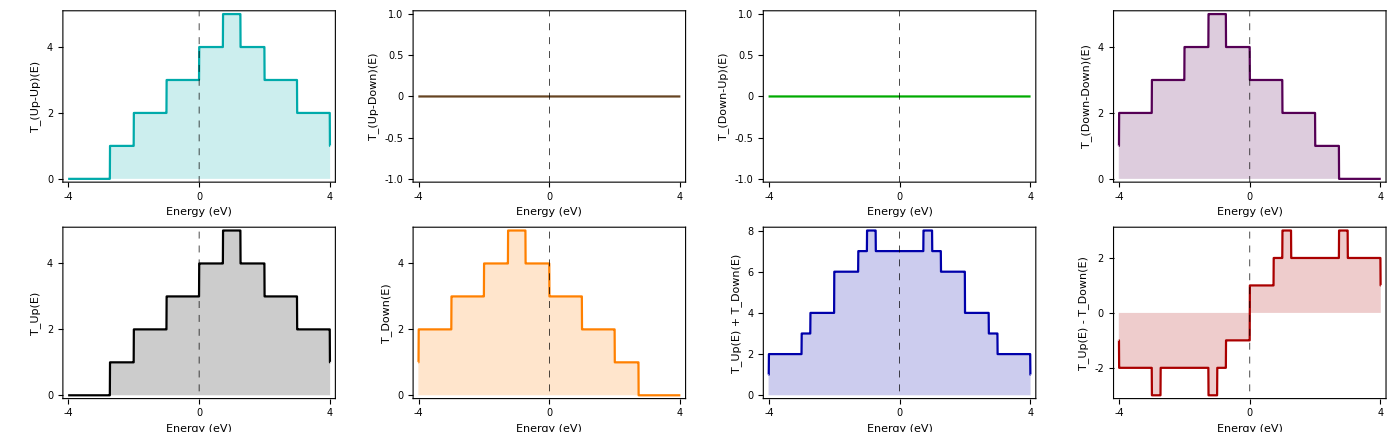

```mathematica
(******************************************* System Parameters ************************************************)
h=1.;r=1;
onsiteChannel={{h,0},{0,-h}}; tHorizontalChannel={{1,0},{0,1}}; tVerticalChannel = {{1,0},{0,1}};
τSC =1.; τCD = τSC; 
tHS=1;tVS=tHS;
onsiteSource={{h,0},{0,-h}}; tHorizontalSource={{tHS,0},{0,tHS}}; tVerticalSource =tHorizontalSource;
onsiteDrain=onsiteSource; tHorizontalDrain=tHorizontalSource; tVerticalDrain = tVerticalSource ;
η=0.00001;
surfaceElements1=Sort@Table[i,{i,1,5}];

(****************************************** system hamiltonian ********************************)
surfaceElements= Sort@Join[surfaceElements1,Table[Length@latticeCoordinates-surfaceElements1[[i]]+1,{i,1,Length@surfaceElements1}]];
Hamiltonian =ArrayFlatten[ Table[If[r==c ,onsiteChannel,If[MemberQ[NNHI[[r,2]],c],tHorizontalChannel,0]],{r, 1, Length@supercellCoordinates},{c, 1, Length@supercellCoordinates}]];

(***************************************** Couplings ******************************************)
τSource =ArrayFlatten[ Table[If[Hamiltonian[[r,c+2  Max[surfaceElements1]]]==0,0,τSC],{r,2*Length@surfaceElements1},{c,2*Length@surfaceElements1}]];
τDrain = τSource;

(**********************************Leads******************************************)
alphaSource =ArrayFlatten[Table[If[r==c,onsiteSource,If[MemberQ[NNHI[[r,2]],c],tHorizontalSource,0]],{r, 1, Length@surfaceElements1},{c, 1, Length@surfaceElements1}]];
alphaDrain= alphaSource ;

τ0Source=ArrayFlatten[Table[If[PossibleZeroQ[Hamiltonian[[r,c+2 Max[surfaceElements1]]]],0,tHS],{r,2 *Length@surfaceElements1},{c,2*Length@surfaceElements1}]];
τ0Drain=τ0Source;

Map[MatrixForm,{Hamiltonian,τSource, alphaSource, τ0Source}];

E1=0;
transmission =ParallelTable[
(******************************************* Self energy for Source ************************************************)
gS11=Inverse[(E1+ⅈ η) IdentityMatrix[Length@alphaSource ]-alphaSource ]; (*Surface Green's function*)
GS11=Array[x,{Length@alphaSource,Length@alphaSource}]; (*Solve dyson equation*)
f=(gS11.ConjugateTranspose[τ0Source].GS11.τ0Source-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@alphaSource *Length@alphaSource }]];
ΣS = ArrayFlatten[Table[If[i==j==1,ConjugateTranspose[τSource].Partition[Values[sol],{Length@τSource}].τSource,0],{i,1,Length@Hamiltonian-(2 Length@surfaceElements1-1)},{j,1,Length@Hamiltonian-(2 Length@surfaceElements1-1)}]];
ΓS =-2Im[ΣS];
ΓSUp=Table[If[OddQ[r],-2 Im[ΣS[[r,c]]],0],{r, Length@ΣS},{c, Length@ΣS}];
          ΓSDw=Table[If[EvenQ[r],-2 Im[ΣS[[r,c]]],0],{r, Length@ΣS},{c, Length@ΣS}];
(******************************************* Self energy for Drain ************************************************)
gS11=Inverse[(E1+ⅈ η) IdentityMatrix[Length@alphaDrain]-alphaDrain ]; (*Surface Green's function*)
GS11=Array[x,{Length@alphaDrain,Length@alphaDrain}]; (*Solve dyson equation*)
f=(gS11.τ0Drain.GS11.ConjugateTranspose[τ0Drain]-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@alphaDrain*Length@alphaDrain }]];
ΣD = ArrayFlatten[Table[If[i==j==Length@Hamiltonian-(2 Length@surfaceElements1-1),τDrain.Partition[Values[sol],{Length@τDrain}].ConjugateTranspose[τDrain],0],{i,1,Length@Hamiltonian-(2 Length@surfaceElements1-1)},{j,1,Length@Hamiltonian-(2 Length@surfaceElements1-1)}]];
ΓD=-2Im[ΣD];
ΓDUp=Table[If[OddQ[r],-2 Im[ΣD[[r,c]]],0],{r, Length@ΣD},{c, Length@ΣD}];
	 ΓDDw=Table[If[EvenQ[r],-2 Im[ΣD[[r,c]]],0],{r, Length@ΣD},{c, Length@ΣD}];
(*Print[ΣS //Length," ",ΣD//Length," ",ΓS//Length," ",ΓD//Length," ",Length@Hamiltonian];
Print[ΣS //MatrixForm,ΣD//MatrixForm,ΓS//MatrixForm,ΓD//MatrixForm];
Map[MatrixForm,{ΓSUp,ΓSDw,ΓDUp,ΓDDw}]*)
(******************************************* Green's function and Transmission ************************************************)
GR=Inverse[E1 IdentityMatrix[Length@Hamiltonian]-Hamiltonian-ΣS-ΣD];
GA=ConjugateTranspose[GR];
(*Print[Chop[Tr[ΓSUp.GR.ΓDUp.GA]]," ", Chop[Tr[ΓSUp.GR.ΓDDw.GA]]," ",Chop[Tr[ΓSDw.GR.ΓDUp.GA]]," ",Chop[Tr[ΓSDw.GR.ΓDDw.GA]]];*)
{E1, Chop[Tr[ΓSUp.GR.ΓDUp.GA]],Chop[Tr[ΓSUp.GR.ΓDDw.GA]],Chop[Tr[ΓSDw.GR.ΓDUp.GA]],Chop[Tr[ΓSDw.GR.ΓDDw.GA]],Chop[Tr[ΓSUp.GR.ΓDUp.GA]]+Chop[Tr[ΓSDw.GR.ΓDUp.GA]],Chop[Tr[ΓSUp.GR.ΓDDw.GA]]+Chop[Tr[ΓSDw.GR.ΓDDw.GA]],Chop[Tr[ΓSUp.GR.ΓDUp.GA]]+Chop[Tr[ΓSDw.GR.ΓDUp.GA]]+Chop[Tr[ΓSUp.GR.ΓDDw.GA]]+Chop[Tr[ΓSDw.GR.ΓDDw.GA]],Chop[Chop[Tr[ΓSUp.GR.ΓDUp.GA]]+Chop[Tr[ΓSDw.GR.ΓDUp.GA]]-Chop[Tr[ΓSUp.GR.ΓDDw.GA]]-Chop[Tr[ΓSDw.GR.ΓDDw.GA]]]},{E1,-4.01,4.01,0.0057}];

tickFunction=Charting`ScaledTicks[{Identity,Identity},"TicksLength"->{.02,.01}][##,{5,1}]&;
TUU = ListLinePlot[transmission[[All,{1,2}]],Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Darker[Cyan]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T_(Up-Up)(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]];
TUD = ListLinePlot[transmission[[All,{1,3}]],Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Darker[Brown]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T_(Up-Down)(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]];
TDU = ListLinePlot[transmission[[All,{1,4}]],Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Darker[Green]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T_(Down-Up)(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]];
TDD = ListLinePlot[transmission[[All,{1,5}]],Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Darker[Purple]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T_(Down-Down)(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]];
TU = ListLinePlot[transmission[[All,{1,6}]],Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Darker[Black]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T_Up(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]];
TD = ListLinePlot[transmission[[All,{1,7}]],Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Orange],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T_Down(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]];
TUPlusD = ListLinePlot[transmission[[All,{1,8}]],Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Darker[Blue]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T_Up(E) + T_Down(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]];
TUMinusD = ListLinePlot[transmission[[All,{1,9}]],Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Darker[Red]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T_Up(E) - T_Down(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]];
GraphicsGrid[{{TUU,TUD,TDU,TDD},{TU,TD,TUPlusD,TUMinusD}},Spacings->1,ImageSize->1400]
```

## Graphene (Spin-less)

### Zigzag

#### Model

```mathematica
(****************************************** Function to generate a supercell ******************************************)
GenerateSupercell[atoms_,a1_,a2_,nx_,ny_]:=Module[{supercell},
supercell=Flatten[Table[(#+n a1+m a2)&/@atoms,{n,0,nx-1},{m,0,ny-1}],2];
supercell];
GroupAtomsByDistance[coordinates_,minDist_,maxDist_]:=Module[{pairs},pairs=Select[Subsets[coordinates,{2}],(*Generate all pairs of coordinates*)minDist<EuclideanDistance[#[[1]],#[[2]]]<maxDist&];
pairs];

(******************************************  Generate a NxN supercell and Plot *****************************************)
atomPositions = {{(√3)/2,-1},{0,-1/2},{0,1/2},{(√3)/2,1}};
ax = {√3,0};
ay = {0,3};
nx=4; ny=2;
supercellCoordinates=GenerateSupercell[atomPositions,ax,ay,nx,ny];
hoppings=GroupAtomsByDistance[supercellCoordinates,0.9,1.1];

Show[Table[Graphics3D[{Red,Specularity[White,20],Sphere[Append[supercellCoordinates[[i]],0],0.2]},Boxed->False],{i,1,Length@supercellCoordinates}],Table[Graphics3D[{RGBColor[0.04,0.38,1.],Specularity[White,20],Cylinder[Append[#,0]&/@hoppings[[i,1;;2]],0.07]},Boxed->False],{i,1,Length@hoppings}],Table[Graphics3D[Text[Style[i,20,White],Append[supercellCoordinates[[i]],0]]],{i,1,Length[supercellCoordinates]}],ViewPoint->Above,ImageSize->400]

(******************************* nearest neighbors *******************************)
nearestNeighbors[latticeCoordinates_]:=Table[{point,Select[latticeCoordinates,0<EuclideanDistance[#,point]<= 1.1&]},{point,latticeCoordinates}]
nearestNeighborsIndex[latticeCoordinates_]:=Table[{First@First@Position[latticeCoordinates,point],Flatten[First@Position[latticeCoordinates,#]&/@Select[latticeCoordinates,0<EuclideanDistance[#,point]<=1.1&]]},{point,latticeCoordinates}]
NNH=nearestNeighbors[supercellCoordinates];
NNHI=nearestNeighborsIndex[supercellCoordinates]
```

-Graphics3D-

{{1,{2,10}},{2,{1,3}},{3,{2,4}},{4,{3,5,11}},{5,{4,6,14}},{6,{5,7}},{7,{6,8}},{8,{7,15}},{9,{10,18}},{10,{1,9,11}},{11,{4,10,12}},{12,{11,13,19}},{13,{12,14,22}},{14,{5,13,15}},{15,{8,14,16}},{16,{15,23}},{17,{18,26}},{18,{9,17,19}},{19,{12,18,20}},{20,{19,21,27}},{21,{20,22,30}},{22,{13,21,23}},{23,{16,22,24}},{24,{23,31}},{25,{26}},{26,{17,25,27}},{27,{20,26,28}},{28,{27,29}},{29,{28,30}},{30,{21,29,31}},{31,{24,30,32}},{32,{31}}}

#### Transmission

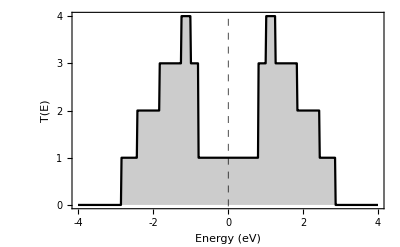

```mathematica
(******************************************* System Parameters ************************************************)
onsiteChannel=0; tHorizontalChannel=1; tVerticalChannel = 1;
τSC = 1; τCD = τSC; 
onsiteSource=0; tHorizontalSource=1.; tVerticalSource = 1;
onsiteDrain=onsiteSource; tHorizontalDrain=tHorizontalSource; tVerticalDrain = tVerticalSource ;
η=0.00001;
surfaceElements1=Sort@Table[i,{i,1,8}];

(****************************************** system hamiltonian ********************************)
surfaceElements= Sort@Join[surfaceElements1,Table[Length@latticeCoordinates-surfaceElements1[[i]]+1,{i,1,Length@surfaceElements1}]];
Hamiltonian = Table[If[r==c ,onsiteChannel,If[MemberQ[NNHI[[r,2]],c],tHorizontalChannel,0]],{r, 1, Length@supercellCoordinates},{c, 1, Length@supercellCoordinates}];

(***************************************** Couplings ******************************************)
τSource = Table[If[PossibleZeroQ[Hamiltonian[[r,c+Max[surfaceElements1]]]],0,τSC],{r,surfaceElements1},{c,surfaceElements1}]; (*Coupling between source to channel*)
τDrain = τSource;

(**********************************Leads******************************************)
alphaSource =Table[If[r==c,onsiteSource,If[MemberQ[NNHI[[r,2]],c],tHorizontalSource,0]],{r, 1, Length@surfaceElements1},{c, 1, Length@surfaceElements1}];
alphaDrain= alphaSource ;

τ0Source=Table[If[PossibleZeroQ[Hamiltonian[[r,c+Max[surfaceElements1]]]],0,tHorizontalSource],{r,surfaceElements1},{c,surfaceElements1}];
τ0Drain=τ0Source;

Map[MatrixForm,{Hamiltonian,τSource, alphaSource, τ0Source}];

E1=0.;
transmission =ParallelTable[
(******************************************* Self energy for Source ************************************************)
gS11=Inverse[(E1+ⅈ η) IdentityMatrix[Length@alphaSource ]-alphaSource ]; (*Surface Green's function*)
GS11=Array[x,{Length@alphaSource,Length@alphaSource}]; (*Solve dyson equation*)
f=(gS11.ConjugateTranspose[τ0Source].GS11.τ0Source-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@alphaSource *Length@alphaSource }]];
ΣS = ArrayFlatten[Table[If[i==j==1,ConjugateTranspose[τSource].Partition[Values[sol],{Length@τSource}].τSource,0],{i,1,Length@Hamiltonian-(Length@surfaceElements1-1)},{j,1,Length@Hamiltonian-(Length@surfaceElements1-1)}]];
ΓS =-2Im[ΣS];
(******************************************* Self energy for Drain ************************************************)
gS11=Inverse[(E1+ⅈ η) IdentityMatrix[Length@alphaDrain]-alphaDrain ]; (*Surface Green's function*)
GS11=Array[x,{Length@alphaDrain,Length@alphaDrain}]; (*Solve dyson equation*)
f=(gS11.τ0Drain.GS11.ConjugateTranspose[τ0Drain]-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@alphaDrain*Length@alphaDrain }]];
ΣD = ArrayFlatten[Table[If[i==j==Length@Hamiltonian-(Length@surfaceElements1-1),τDrain.Partition[Values[sol],{Length@τDrain}].ConjugateTranspose[τDrain],0],{i,1,Length@Hamiltonian-(Length@surfaceElements1-1)},{j,1,Length@Hamiltonian-(Length@surfaceElements1-1)}]];
ΓD=-2Im[ΣD];
(*Print[ΣS //Length," ",ΣD//Length," ",ΓS//Length," ",ΓD//Length," ",Length@Hamiltonian]*)
(*Print[ΣS //MatrixForm,ΣD//MatrixForm,ΓS//MatrixForm,ΓD//MatrixForm]*)
(******************************************* Green's function and Transmission ************************************************)
GR=Inverse[E1 IdentityMatrix[Length@Hamiltonian]-Hamiltonian-ΣS-ΣD];
GA=ConjugateTranspose[GR];
{E1, Chop[ Tr[ΓS.GR.ΓD.GA]]},{E1,-4.01,4.01,0.0157}];

tickFunction=Charting`ScaledTicks[{Identity,Identity},"TicksLength"->{.02,.01}][##,{5,1}]&;
ListLinePlot[transmission,Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Darker[Black]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]]
Map[MatrixForm,{ΓS,ΓD}];
```

### Armchair

#### Model

```mathematica
atomPositions = {{-1,0},{-1/2,-(√3)/2},{1/2,-(√3)/2},{1,0}};
ax = {3,0};
ay = {0,√3};

(*Function to generate a supercell*)
GenerateSupercell[atoms_,a1_,a2_,nx_,ny_]:=Module[{supercell},
supercell=Flatten[Table[(#+n a1+m a2)&/@atoms,{n,0,nx-1},{m,0,ny-1}],2];
supercell];
GroupAtomsByDistance[coordinates_,minDist_,maxDist_]:=Module[{pairs},pairs=Select[Subsets[coordinates,{2}],(*Generate all pairs of coordinates*)minDist<EuclideanDistance[#[[1]],#[[2]]]<maxDist&];
pairs];

(*Generate a 3x3 supercell*)
nx=4; ny=3;
supercellCoordinates=SortBy[GenerateSupercell[atomPositions,ax,ay,nx,ny],First];
hoppings=GroupAtomsByDistance[supercellCoordinates,0.9,1.1];

(*Plot the supercell*)
Show[Table[Graphics3D[{Red,Specularity[White,20],Sphere[Append[supercellCoordinates[[i]],0],0.2]},Boxed->False],{i,1,Length@supercellCoordinates}],Table[Graphics3D[{RGBColor[0.04,0.38,1.],Specularity[White,20],Cylinder[Append[#,0]&/@hoppings[[i,1;;2]],0.07]},Boxed->False],{i,1,Length@hoppings}],Table[Graphics3D[Text[Style[i,20,White],Append[supercellCoordinates[[i]],0]]],{i,1,Length[supercellCoordinates]}],ViewPoint->Above,ImageSize->700]

(******************************* nearest neighbors *******************************)
nearestNeighbors[latticeCoordinates_]:=Table[{point,Select[latticeCoordinates,0<EuclideanDistance[#,point]<= 1.1&]},{point,latticeCoordinates}]
nearestNeighborsIndex[latticeCoordinates_]:=Table[{First@First@Position[latticeCoordinates,point],Flatten[First@Position[latticeCoordinates,#]&/@Select[latticeCoordinates,0<EuclideanDistance[#,point]<=1.1&]]},{point,latticeCoordinates}]
NNH=nearestNeighbors[supercellCoordinates];
NNHI=nearestNeighborsIndex[supercellCoordinates]
```

-Graphics3D-

{{1,{4,5}},{2,{5,6}},{3,{6}},{4,{1,7}},{5,{1,2,8}},{6,{2,3,9}},{7,{4,10}},{8,{5,10,11}},{9,{6,11,12}},{10,{7,8,13}},{11,{8,9,14}},{12,{9,15}},{13,{10,16,17}},{14,{11,17,18}},{15,{12,18}},{16,{13,19}},{17,{13,14,20}},{18,{14,15,21}},{19,{16,22}},{20,{17,22,23}},{21,{18,23,24}},{22,{19,20,25}},{23,{20,21,26}},{24,{21,27}},{25,{22,28,29}},{26,{23,29,30}},{27,{24,30}},{28,{25,31}},{29,{25,26,32}},{30,{26,27,33}},{31,{28,34}},{32,{29,34,35}},{33,{30,35,36}},{34,{31,32,37}},{35,{32,33,38}},{36,{33,39}},{37,{34,40,41}},{38,{35,41,42}},{39,{36,42}},{40,{37,43}},{41,{37,38,44}},{42,{38,39,45}},{43,{40,46}},{44,{41,46,47}},{45,{42,47,48}},{46,{43,44}},{47,{44,45}},{48,{45}}}

#### Transmission

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

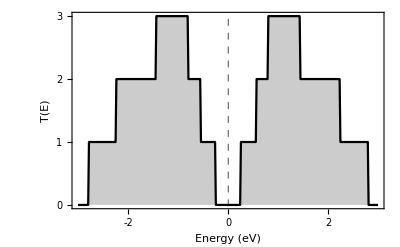

```mathematica
(******************************************* System Parameters ************************************************)
onsiteChannel=0; tHorizontalChannel=1; tVerticalChannel = 1;
τSC = 1.; τCD = τSC; 
onsiteSource=0.; tHorizontalSource=1.; tVerticalSource = 1;
onsiteDrain=onsiteSource; tHorizontalDrain=tHorizontalSource; tVerticalDrain = tVerticalSource ;
η=0.00001;
surfaceElements1=Sort@Table[i,{i,1,12}];

(****************************************** system hamiltonian ********************************)
surfaceElements= Sort@Join[surfaceElements1,Table[Length@supercellCoordinates-surfaceElements1[[i]]+1,{i,1,Length@surfaceElements1}]];
Hamiltonian = Table[If[r==c ,onsiteChannel,If[MemberQ[NNHI[[r,2]],c],tHorizontalChannel,0]],{r, 1, Length@supercellCoordinates},{c, 1, Length@supercellCoordinates}];

(***************************************** Couplings ******************************************)
τSource = Table[If[PossibleZeroQ[Hamiltonian[[r,c+Max[surfaceElements1]]]],0,τSC],{r,surfaceElements1},{c,surfaceElements1}]; (*Coupling between source to channel*)
τDrain = τSource;

(**********************************Leads******************************************)
alphaSource =Table[If[r==c,onsiteSource,If[MemberQ[NNHI[[r,2]],c],tHorizontalSource,0]],{r, 1, Length@surfaceElements1},{c, 1, Length@surfaceElements1}];
alphaDrain= alphaSource ;

τ0Source=Table[If[PossibleZeroQ[Hamiltonian[[r,c+Max[surfaceElements1]]]],0,tHorizontalSource],{r,surfaceElements1},{c,surfaceElements1}];
τ0Drain=τ0Source;

Map[MatrixForm,{Hamiltonian,τSource, alphaSource, τ0Source}];

E1=0.;
transmission =ParallelTable[
(******************************************* Self energy for Source ************************************************)
gS11=Inverse[(E1+ⅈ η) IdentityMatrix[Length@alphaSource ]-alphaSource ]; (*Surface Green's function*)
GS11=Array[x,{Length@alphaSource,Length@alphaSource}]; (*Solve dyson equation*)
f=(gS11.ConjugateTranspose[τ0Source].GS11.τ0Source-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@alphaSource *Length@alphaSource }]];
ΣS = ArrayFlatten[Table[If[i==j==1,ConjugateTranspose[τSource].Partition[Values[sol],{Length@τSource}].τSource,0],{i,1,Length@Hamiltonian-(Length@surfaceElements1-1)},{j,1,Length@Hamiltonian-(Length@surfaceElements1-1)}]];
ΓS =-2Im[ΣS];
(******************************************* Self energy for Drain ************************************************)
gS11=Inverse[(E1+ⅈ η) IdentityMatrix[Length@alphaDrain]-alphaDrain ]; (*Surface Green's function*)
GS11=Array[x,{Length@alphaDrain,Length@alphaDrain}]; (*Solve dyson equation*)
f=(gS11.τ0Drain.GS11.ConjugateTranspose[τ0Drain]-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@alphaDrain*Length@alphaDrain }]];
ΣD = ArrayFlatten[Table[If[i==j==Length@Hamiltonian-(Length@surfaceElements1-1),τDrain.Partition[Values[sol],{Length@τDrain}].ConjugateTranspose[τDrain],0],{i,1,Length@Hamiltonian-(Length@surfaceElements1-1)},{j,1,Length@Hamiltonian-(Length@surfaceElements1-1)}]];
ΓD=-2Im[ΣD];
(*Print[ΣS //Length," ",ΣD//Length," ",ΓS//Length," ",ΓD//Length," ",Length@Hamiltonian]*)
(*Print[ΣS //MatrixForm,ΣD//MatrixForm,ΓS//MatrixForm,ΓD//MatrixForm]*)
(******************************************* Green's function and Transmission ************************************************)
GR=Inverse[E1 IdentityMatrix[Length@Hamiltonian]-Hamiltonian-ΣS-ΣD];
GA=ConjugateTranspose[GR];
{E1, Chop[ Tr[ΓS.GR.ΓD.GA]]},{E1,-3.01,3.01,0.0157}];

tickFunction=Charting`ScaledTicks[{Identity,Identity},"TicksLength"->{.02,.01}][##,{5,1}]&;
ListLinePlot[transmission,Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Darker[Black]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]]
Map[MatrixForm,{ΓS,ΓD}];
```

## Graphene (Spin-full )

### Zigzag

#### Model

```mathematica
(****************************************** Function to generate a supercell ******************************************)
GenerateSupercell[atoms_,a1_,a2_,nx_,ny_]:=Module[{supercell},
supercell=Flatten[Table[(#+n a1+m a2)&/@atoms,{n,0,nx-1},{m,0,ny-1}],2];
supercell];
GroupAtomsByDistance[coordinates_,minDist_,maxDist_]:=Module[{pairs},pairs=Select[Subsets[coordinates,{2}],(*Generate all pairs of coordinates*)minDist<EuclideanDistance[#[[1]],#[[2]]]<maxDist&];
pairs];

(******************************************  Generate a NxN supercell and Plot *****************************************)
atomPositions = {{(√3)/2,-1},{0,-1/2},{0,1/2},{(√3)/2,1}};
ax = {√3,0};
ay = {0,3};
nx=5; ny=2;
supercellCoordinates=GenerateSupercell[atomPositions,ax,ay,nx,ny];
hoppings=GroupAtomsByDistance[supercellCoordinates,0.9,1.1];

Show[Table[Graphics3D[{Red,Specularity[White,20],Sphere[Append[supercellCoordinates[[i]],0],0.2]},Boxed->False],{i,1,Length@supercellCoordinates}],Table[Graphics3D[{RGBColor[0.04,0.38,1.],Specularity[White,20],Cylinder[Append[#,0]&/@hoppings[[i,1;;2]],0.07]},Boxed->False],{i,1,Length@hoppings}],Table[Graphics3D[Text[Style[i,20,White],Append[supercellCoordinates[[i]],0]]],{i,1,Length[supercellCoordinates]}],ViewPoint->Above,ImageSize->400]

(******************************* nearest neighbors *******************************)
nearestNeighbors[latticeCoordinates_]:=Table[{point,Select[latticeCoordinates,0<EuclideanDistance[#,point]<= 1.1&]},{point,latticeCoordinates}]
nearestNeighborsIndex[latticeCoordinates_]:=Table[{First@First@Position[latticeCoordinates,point],Flatten[First@Position[latticeCoordinates,#]&/@Select[latticeCoordinates,0<EuclideanDistance[#,point]<=1.1&]]},{point,latticeCoordinates}]
NNH=nearestNeighbors[supercellCoordinates];
NNHI=nearestNeighborsIndex[supercellCoordinates]
```

-Graphics3D-

{{1,{2,10}},{2,{1,3}},{3,{2,4}},{4,{3,5,11}},{5,{4,6,14}},{6,{5,7}},{7,{6,8}},{8,{7,15}},{9,{10,18}},{10,{1,9,11}},{11,{4,10,12}},{12,{11,13,19}},{13,{12,14,22}},{14,{5,13,15}},{15,{8,14,16}},{16,{15,23}},{17,{18,26}},{18,{9,17,19}},{19,{12,18,20}},{20,{19,21,27}},{21,{20,22,30}},{22,{13,21,23}},{23,{16,22,24}},{24,{23,31}},{25,{26,34}},{26,{17,25,27}},{27,{20,26,28}},{28,{27,29,35}},{29,{28,30,38}},{30,{21,29,31}},{31,{24,30,32}},{32,{31,39}},{33,{34}},{34,{25,33,35}},{35,{28,34,36}},{36,{35,37}},{37,{36,38}},{38,{29,37,39}},{39,{32,38,40}},{40,{39}}}

#### Transmission

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

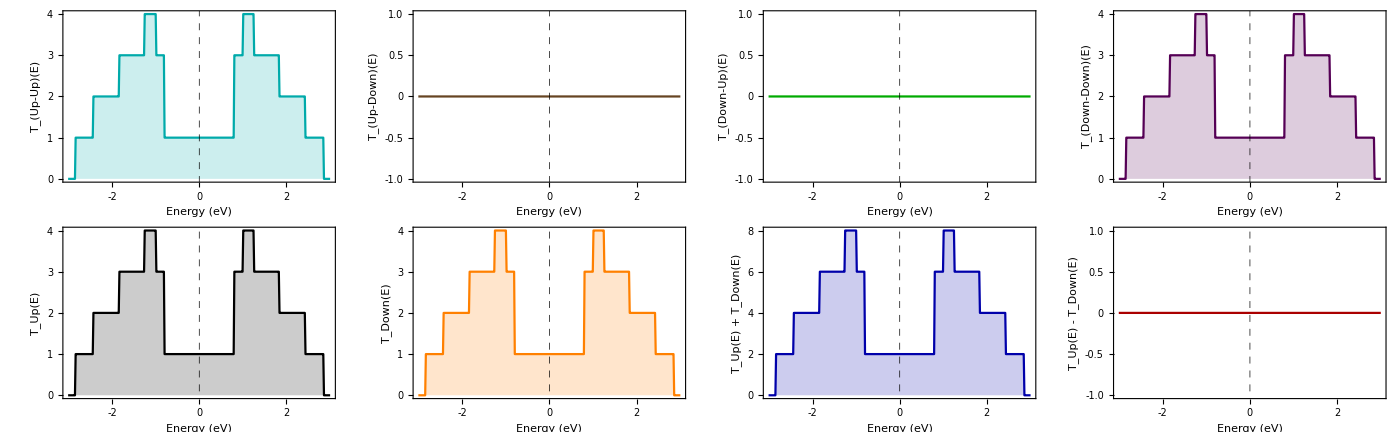

```mathematica
(******************************************* System Parameters ************************************************)
h=0;r=1;
onsiteChannel={{h,0},{0,-h}}; tHorizontalChannel={{1,0},{0,1}}; tVerticalChannel = {{1,0},{0,1}};
τSC =1; τCD = τSC; 
tHS=1;tVS=tHS;
onsiteSource={{h,0},{0,-h}}; tHorizontalSource={{tHS,0},{0,tHS}}; tVerticalSource =tHorizontalSource;
onsiteDrain=onsiteSource; tHorizontalDrain=tHorizontalSource; tVerticalDrain = tVerticalSource ;
η=0.00001;
surfaceElements1=Sort@Table[i,{i,1,8}];

(****************************************** system hamiltonian ********************************)
surfaceElements= Sort@Join[surfaceElements1,Table[Length@latticeCoordinates-surfaceElements1[[i]]+1,{i,1,Length@surfaceElements1}]];
Hamiltonian =ArrayFlatten[ Table[If[r==c ,onsiteChannel,If[MemberQ[NNHI[[r,2]],c],tHorizontalChannel,0]],{r, 1, Length@supercellCoordinates},{c, 1, Length@supercellCoordinates}]];

(***************************************** Couplings ******************************************)
τSource =ArrayFlatten[ Table[If[Hamiltonian[[r,c+2  Max[surfaceElements1]]]==0,0,τSC],{r,2*Length@surfaceElements1},{c,2*Length@surfaceElements1}]];
τDrain = τSource;

(**********************************Leads******************************************)
alphaSource =ArrayFlatten[Table[If[r==c,onsiteSource,If[MemberQ[NNHI[[r,2]],c],tHorizontalSource,0]],{r, 1, Length@surfaceElements1},{c, 1, Length@surfaceElements1}]];
alphaDrain= alphaSource ;

τ0Source=ArrayFlatten[Table[If[PossibleZeroQ[Hamiltonian[[r,c+2 Max[surfaceElements1]]]],0,tHS],{r,2 *Length@surfaceElements1},{c,2*Length@surfaceElements1}]];
τ0Drain=τ0Source;

Map[MatrixForm,{Hamiltonian,τSource, alphaSource, τ0Source}];

E1=0;
transmission =ParallelTable[
(******************************************* Self energy for Source ************************************************)
gS11=Inverse[(E1+ⅈ η) IdentityMatrix[Length@alphaSource ]-alphaSource ]; (*Surface Green's function*)
GS11=Array[x,{Length@alphaSource,Length@alphaSource}]; (*Solve dyson equation*)
f=(gS11.ConjugateTranspose[τ0Source].GS11.τ0Source-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@alphaSource *Length@alphaSource }]];
ΣS = ArrayFlatten[Table[If[i==j==1,ConjugateTranspose[τSource].Partition[Values[sol],{Length@τSource}].τSource,0],{i,1,Length@Hamiltonian-(2 Length@surfaceElements1-1)},{j,1,Length@Hamiltonian-(2 Length@surfaceElements1-1)}]];
ΓS =-2Im[ΣS];
ΓSUp=Table[If[OddQ[r],-2 Im[ΣS[[r,c]]],0],{r, Length@ΣS},{c, Length@ΣS}];
          ΓSDw=Table[If[EvenQ[r],-2 Im[ΣS[[r,c]]],0],{r, Length@ΣS},{c, Length@ΣS}];
(******************************************* Self energy for Drain ************************************************)
gS11=Inverse[(E1+ⅈ η) IdentityMatrix[Length@alphaDrain]-alphaDrain ]; (*Surface Green's function*)
GS11=Array[x,{Length@alphaDrain,Length@alphaDrain}]; (*Solve dyson equation*)
f=(gS11.τ0Drain.GS11.ConjugateTranspose[τ0Drain]-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@alphaDrain*Length@alphaDrain }]];
ΣD = ArrayFlatten[Table[If[i==j==Length@Hamiltonian-(2 Length@surfaceElements1-1),τDrain.Partition[Values[sol],{Length@τDrain}].ConjugateTranspose[τDrain],0],{i,1,Length@Hamiltonian-(2 Length@surfaceElements1-1)},{j,1,Length@Hamiltonian-(2 Length@surfaceElements1-1)}]];
ΓD=-2Im[ΣD];
ΓDUp=Table[If[OddQ[r],-2 Im[ΣD[[r,c]]],0],{r, Length@ΣD},{c, Length@ΣD}];
	 ΓDDw=Table[If[EvenQ[r],-2 Im[ΣD[[r,c]]],0],{r, Length@ΣD},{c, Length@ΣD}];
(*Print[ΣS //Length," ",ΣD//Length," ",ΓS//Length," ",ΓD//Length," ",Length@Hamiltonian];
Print[ΣS //MatrixForm,ΣD//MatrixForm,ΓS//MatrixForm,ΓD//MatrixForm];
Map[MatrixForm,{ΓSUp,ΓSDw,ΓDUp,ΓDDw}]*)
(******************************************* Green's function and Transmission ************************************************)
GR=Inverse[E1 IdentityMatrix[Length@Hamiltonian]-Hamiltonian-ΣS-ΣD];
GA=ConjugateTranspose[GR];
(*Print[Chop[Tr[ΓSUp.GR.ΓDUp.GA]]," ", Chop[Tr[ΓSUp.GR.ΓDDw.GA]]," ",Chop[Tr[ΓSDw.GR.ΓDUp.GA]]," ",Chop[Tr[ΓSDw.GR.ΓDDw.GA]]];*)
{E1, Chop[Tr[ΓSUp.GR.ΓDUp.GA]],Chop[Tr[ΓSUp.GR.ΓDDw.GA]],Chop[Tr[ΓSDw.GR.ΓDUp.GA]],Chop[Tr[ΓSDw.GR.ΓDDw.GA]],Chop[Tr[ΓSUp.GR.ΓDUp.GA]]+Chop[Tr[ΓSDw.GR.ΓDUp.GA]],Chop[Tr[ΓSUp.GR.ΓDDw.GA]]+Chop[Tr[ΓSDw.GR.ΓDDw.GA]],Chop[Tr[ΓSUp.GR.ΓDUp.GA]]+Chop[Tr[ΓSDw.GR.ΓDUp.GA]]+Chop[Tr[ΓSUp.GR.ΓDDw.GA]]+Chop[Tr[ΓSDw.GR.ΓDDw.GA]],Chop[Chop[Tr[ΓSUp.GR.ΓDUp.GA]]+Chop[Tr[ΓSDw.GR.ΓDUp.GA]]-Chop[Tr[ΓSUp.GR.ΓDDw.GA]]-Chop[Tr[ΓSDw.GR.ΓDDw.GA]]]},{E1,-3.01,3.01,0.0157}];

tickFunction=Charting`ScaledTicks[{Identity,Identity},"TicksLength"->{.02,.01}][##,{5,1}]&;
TUU = ListLinePlot[transmission[[All,{1,2}]],Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Darker[Cyan]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T_(Up-Up)(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]];
TUD = ListLinePlot[transmission[[All,{1,3}]],Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Darker[Brown]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T_(Up-Down)(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]];
TDU = ListLinePlot[transmission[[All,{1,4}]],Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Darker[Green]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T_(Down-Up)(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]];
TDD = ListLinePlot[transmission[[All,{1,5}]],Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Darker[Purple]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T_(Down-Down)(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]];
TU = ListLinePlot[transmission[[All,{1,6}]],Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Darker[Black]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T_Up(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]];
TD = ListLinePlot[transmission[[All,{1,7}]],Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Orange],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T_Down(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]];
TUPlusD = ListLinePlot[transmission[[All,{1,8}]],Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Darker[Blue]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T_Up(E) + T_Down(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]];
TUMinusD = ListLinePlot[transmission[[All,{1,9}]],Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Darker[Red]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T_Up(E) - T_Down(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]];
GraphicsGrid[{{TUU,TUD,TDU,TDD},{TU,TD,TUPlusD,TUMinusD}},Spacings->1,ImageSize->1400]
```

### Armchair

#### Model

```mathematica
atomPositions = {{-1,0},{-1/2,-(√3)/2},{1/2,-(√3)/2},{1,0}};
ax = {3,0};
ay = {0,√3};

(*Function to generate a supercell*)
GenerateSupercell[atoms_,a1_,a2_,nx_,ny_]:=Module[{supercell},
supercell=Flatten[Table[(#+n a1+m a2)&/@atoms,{n,0,nx-1},{m,0,ny-1}],2];
supercell];
GroupAtomsByDistance[coordinates_,minDist_,maxDist_]:=Module[{pairs},pairs=Select[Subsets[coordinates,{2}],(*Generate all pairs of coordinates*)minDist<EuclideanDistance[#[[1]],#[[2]]]<maxDist&];
pairs];

(*Generate a 3x3 supercell*)
nx=4; ny=3;
supercellCoordinates=SortBy[GenerateSupercell[atomPositions,ax,ay,nx,ny],First];
hoppings=GroupAtomsByDistance[supercellCoordinates,0.9,1.1];

(*Plot the supercell*)
Show[Table[Graphics3D[{Red,Specularity[White,20],Sphere[Append[supercellCoordinates[[i]],0],0.2]},Boxed->False],{i,1,Length@supercellCoordinates}],Table[Graphics3D[{RGBColor[0.04,0.38,1.],Specularity[White,20],Cylinder[Append[#,0]&/@hoppings[[i,1;;2]],0.07]},Boxed->False],{i,1,Length@hoppings}],Table[Graphics3D[Text[Style[i,20,White],Append[supercellCoordinates[[i]],0]]],{i,1,Length[supercellCoordinates]}],ViewPoint->Above,ImageSize->700]

(******************************* nearest neighbors *******************************)
nearestNeighbors[latticeCoordinates_]:=Table[{point,Select[latticeCoordinates,0<EuclideanDistance[#,point]<= 1.1&]},{point,latticeCoordinates}]
nearestNeighborsIndex[latticeCoordinates_]:=Table[{First@First@Position[latticeCoordinates,point],Flatten[First@Position[latticeCoordinates,#]&/@Select[latticeCoordinates,0<EuclideanDistance[#,point]<=1.1&]]},{point,latticeCoordinates}]
NNH=nearestNeighbors[supercellCoordinates];
NNHI=nearestNeighborsIndex[supercellCoordinates]
```

-Graphics3D-

{{1,{4,5}},{2,{5,6}},{3,{6}},{4,{1,7}},{5,{1,2,8}},{6,{2,3,9}},{7,{4,10}},{8,{5,10,11}},{9,{6,11,12}},{10,{7,8,13}},{11,{8,9,14}},{12,{9,15}},{13,{10,16,17}},{14,{11,17,18}},{15,{12,18}},{16,{13,19}},{17,{13,14,20}},{18,{14,15,21}},{19,{16,22}},{20,{17,22,23}},{21,{18,23,24}},{22,{19,20,25}},{23,{20,21,26}},{24,{21,27}},{25,{22,28,29}},{26,{23,29,30}},{27,{24,30}},{28,{25,31}},{29,{25,26,32}},{30,{26,27,33}},{31,{28,34}},{32,{29,34,35}},{33,{30,35,36}},{34,{31,32,37}},{35,{32,33,38}},{36,{33,39}},{37,{34,40,41}},{38,{35,41,42}},{39,{36,42}},{40,{37,43}},{41,{37,38,44}},{42,{38,39,45}},{43,{40,46}},{44,{41,46,47}},{45,{42,47,48}},{46,{43,44}},{47,{44,45}},{48,{45}}}

#### Transmission

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

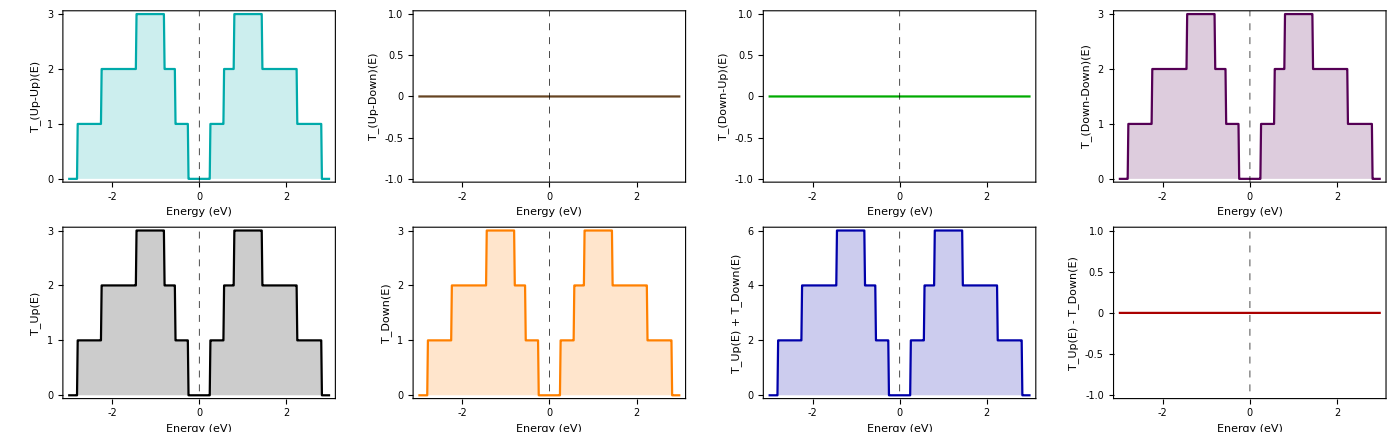

```mathematica
(******************************************* System Parameters ************************************************)
h=0;r=1;
onsiteChannel={{h,0},{0,-h}}; tHorizontalChannel={{1,0},{0,1}}; tVerticalChannel = {{1,0},{0,1}};
τSC =1; τCD = τSC; 
tHS=1;tVS=tHS;
onsiteSource={{h,0},{0,-h}}; tHorizontalSource={{tHS,0},{0,tHS}}; tVerticalSource =tHorizontalSource;
onsiteDrain=onsiteSource; tHorizontalDrain=tHorizontalSource; tVerticalDrain = tVerticalSource ;
η=0.00001;
surfaceElements1=Sort@Table[i,{i,1,12}];

(****************************************** system hamiltonian ********************************)
surfaceElements= Sort@Join[surfaceElements1,Table[Length@latticeCoordinates-surfaceElements1[[i]]+1,{i,1,Length@surfaceElements1}]];
Hamiltonian =ArrayFlatten[ Table[If[r==c ,onsiteChannel,If[MemberQ[NNHI[[r,2]],c],tHorizontalChannel,0]],{r, 1, Length@supercellCoordinates},{c, 1, Length@supercellCoordinates}]];

(***************************************** Couplings ******************************************)
τSource =ArrayFlatten[ Table[If[Hamiltonian[[r,c+2  Max[surfaceElements1]]]==0,0,τSC],{r,2*Length@surfaceElements1},{c,2*Length@surfaceElements1}]];
τDrain = τSource;

(**********************************Leads******************************************)
alphaSource =ArrayFlatten[Table[If[r==c,onsiteSource,If[MemberQ[NNHI[[r,2]],c],tHorizontalSource,0]],{r, 1, Length@surfaceElements1},{c, 1, Length@surfaceElements1}]];
alphaDrain= alphaSource ;

τ0Source=ArrayFlatten[Table[If[PossibleZeroQ[Hamiltonian[[r,c+2 Max[surfaceElements1]]]],0,tHS],{r,2 *Length@surfaceElements1},{c,2*Length@surfaceElements1}]];
τ0Drain=τ0Source;

Map[MatrixForm,{Hamiltonian,τSource, alphaSource, τ0Source}];

E1=0;
transmission =ParallelTable[
(******************************************* Self energy for Source ************************************************)
gS11=Inverse[(E1+ⅈ η) IdentityMatrix[Length@alphaSource ]-alphaSource ]; (*Surface Green's function*)
GS11=Array[x,{Length@alphaSource,Length@alphaSource}]; (*Solve dyson equation*)
f=(gS11.ConjugateTranspose[τ0Source].GS11.τ0Source-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@alphaSource *Length@alphaSource }]];
ΣS = ArrayFlatten[Table[If[i==j==1,ConjugateTranspose[τSource].Partition[Values[sol],{Length@τSource}].τSource,0],{i,1,Length@Hamiltonian-(2 Length@surfaceElements1-1)},{j,1,Length@Hamiltonian-(2 Length@surfaceElements1-1)}]];
ΓS =-2Im[ΣS];
ΓSUp=Table[If[OddQ[r],-2 Im[ΣS[[r,c]]],0],{r, Length@ΣS},{c, Length@ΣS}];
          ΓSDw=Table[If[EvenQ[r],-2 Im[ΣS[[r,c]]],0],{r, Length@ΣS},{c, Length@ΣS}];
(******************************************* Self energy for Drain ************************************************)
gS11=Inverse[(E1+ⅈ η) IdentityMatrix[Length@alphaDrain]-alphaDrain ]; (*Surface Green's function*)
GS11=Array[x,{Length@alphaDrain,Length@alphaDrain}]; (*Solve dyson equation*)
f=(gS11.τ0Drain.GS11.ConjugateTranspose[τ0Drain]-IdentityMatrix[Length@gS11]).GS11+gS11;
sol=FindRoot[Thread[Flatten[f]==0],Table[{Flatten[GS11][[i]],0},{i,1,Length@alphaDrain*Length@alphaDrain }]];
ΣD = ArrayFlatten[Table[If[i==j==Length@Hamiltonian-(2 Length@surfaceElements1-1),τDrain.Partition[Values[sol],{Length@τDrain}].ConjugateTranspose[τDrain],0],{i,1,Length@Hamiltonian-(2 Length@surfaceElements1-1)},{j,1,Length@Hamiltonian-(2 Length@surfaceElements1-1)}]];
ΓD=-2Im[ΣD];
ΓDUp=Table[If[OddQ[r],-2 Im[ΣD[[r,c]]],0],{r, Length@ΣD},{c, Length@ΣD}];
	 ΓDDw=Table[If[EvenQ[r],-2 Im[ΣD[[r,c]]],0],{r, Length@ΣD},{c, Length@ΣD}];
(*Print[ΣS //Length," ",ΣD//Length," ",ΓS//Length," ",ΓD//Length," ",Length@Hamiltonian];
Print[ΣS //MatrixForm,ΣD//MatrixForm,ΓS//MatrixForm,ΓD//MatrixForm];
Map[MatrixForm,{ΓSUp,ΓSDw,ΓDUp,ΓDDw}]*)
(******************************************* Green's function and Transmission ************************************************)
GR=Inverse[E1 IdentityMatrix[Length@Hamiltonian]-Hamiltonian-ΣS-ΣD];
GA=ConjugateTranspose[GR];
(*Print[Chop[Tr[ΓSUp.GR.ΓDUp.GA]]," ", Chop[Tr[ΓSUp.GR.ΓDDw.GA]]," ",Chop[Tr[ΓSDw.GR.ΓDUp.GA]]," ",Chop[Tr[ΓSDw.GR.ΓDDw.GA]]];*)
{E1, Chop[Tr[ΓSUp.GR.ΓDUp.GA]],Chop[Tr[ΓSUp.GR.ΓDDw.GA]],Chop[Tr[ΓSDw.GR.ΓDUp.GA]],Chop[Tr[ΓSDw.GR.ΓDDw.GA]],Chop[Tr[ΓSUp.GR.ΓDUp.GA]]+Chop[Tr[ΓSDw.GR.ΓDUp.GA]],Chop[Tr[ΓSUp.GR.ΓDDw.GA]]+Chop[Tr[ΓSDw.GR.ΓDDw.GA]],Chop[Tr[ΓSUp.GR.ΓDUp.GA]]+Chop[Tr[ΓSDw.GR.ΓDUp.GA]]+Chop[Tr[ΓSUp.GR.ΓDDw.GA]]+Chop[Tr[ΓSDw.GR.ΓDDw.GA]],Chop[Chop[Tr[ΓSUp.GR.ΓDUp.GA]]+Chop[Tr[ΓSDw.GR.ΓDUp.GA]]-Chop[Tr[ΓSUp.GR.ΓDDw.GA]]-Chop[Tr[ΓSDw.GR.ΓDDw.GA]]]},{E1,-3.01,3.01,0.0157}];

tickFunction=Charting`ScaledTicks[{Identity,Identity},"TicksLength"->{.02,.01}][##,{5,1}]&;
TUU = ListLinePlot[transmission[[All,{1,2}]],Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Darker[Cyan]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T_(Up-Up)(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]];
TUD = ListLinePlot[transmission[[All,{1,3}]],Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Darker[Brown]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T_(Up-Down)(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]];
TDU = ListLinePlot[transmission[[All,{1,4}]],Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Darker[Green]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T_(Down-Up)(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]];
TDD = ListLinePlot[transmission[[All,{1,5}]],Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Darker[Purple]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T_(Down-Down)(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]];
TU = ListLinePlot[transmission[[All,{1,6}]],Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Darker[Black]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T_Up(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]];
TD = ListLinePlot[transmission[[All,{1,7}]],Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Orange],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T_Down(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]];
TUPlusD = ListLinePlot[transmission[[All,{1,8}]],Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Darker[Blue]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T_Up(E) + T_Down(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]];
TUMinusD = ListLinePlot[transmission[[All,{1,9}]],Axes->False,Frame->True,PlotRange->All(*{{-4.1,4.1},{-.1,8.2}}*),PlotStyle->Directive[Bold,Darker[Red]],FrameStyle->Directive[Black,16],FrameLabel->{Style["Energy (eV)",20],Style["T_Up(E) - T_Down(E) ",20]},FrameTicks->Table[tickFunction,2,2],FrameTicksStyle->({#,#}&@{FontSize->20,FontOpacity->0}),ImageSize->400,Filling->Axis,GridLines->{{0}, {}},GridLinesStyle->Directive[Black, Dashed]];
GraphicsGrid[{{TUU,TUD,TDU,TDD},{TU,TD,TUPlusD,TUMinusD}},Spacings->1,ImageSize->1400]
```